```mathematica
SetDirectory[NotebookDirectory[]];
```

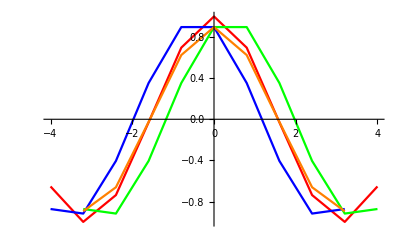
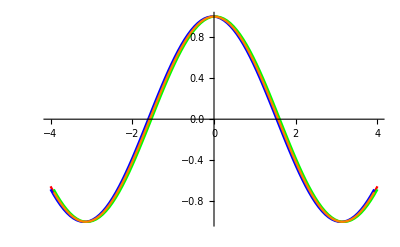
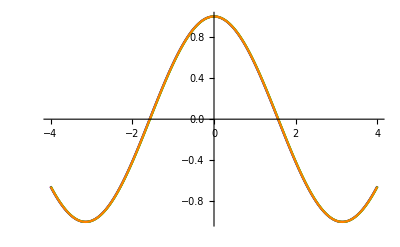

```mathematica
actual = Import["outputs/derivative-10.csv", "CSV"];
forward = Import["outputs/forward-10.csv", "CSV"];
backward = Import["outputs/backward-10.csv", "CSV"];
central = Import["outputs/central-10.csv", "CSV"];
n10 = ListLinePlot[{actual, forward, backward, central}, PlotStyle->{Red, Blue, Green, Orange}];
actual = Import["outputs/derivative-100.csv", "CSV"];
forward = Import["outputs/forward-100.csv", "CSV"];
backward = Import["outputs/backward-100.csv", "CSV"];
central = Import["outputs/central-100.csv", "CSV"];
n100 = ListLinePlot[{actual, forward, backward, central}, PlotStyle->{Red, Blue, Green, Orange}];
actual = Import["outputs/derivative-1000.csv", "CSV"];
forward = Import["outputs/forward-1000.csv", "CSV"];
backward = Import["outputs/backward-1000.csv", "CSV"];
central = Import["outputs/central-1000.csv", "CSV"];
n1000 = ListLinePlot[{actual, forward, backward, central}, PlotStyle->{Red, Blue, Green, Orange}];
{n10, n100, n1000}
```

```mathematica
Manipulate[
Show[Plot[Sin[x],{x,0, π}, PlotRange->{0, 2}], 
Graphics[{
Point[{x0, Sin[x0]}],
Point[{x0+h, Sin[x0+h]}],
Arrow[{
{x0, Sin[x0]}, 
{x0+1,Sin[x0]+(Sin[x0+h]-Sin[x0])/h}
}]}],
Graphics[{
Point[{x0, Sin[x0]}],
Point[{x0-h, Sin[x0-h]}],
Arrow[{
{x0, Sin[x0]}, 
{x0+1,Sin[x0]+(Sin[x0]-Sin[x0-h])/h}
}]}],
Graphics[{
Point[{x0, Sin[x0]}],
Point[{x0-h, Sin[x0-h]}],
Arrow[{
{x0, Sin[x0]}, 
{x0+1,Sin[x0]+(Sin[x0+h]-Sin[x0-h])/(2h)}
}]}]
]
,{h, 0.00001, π}, {{x0, π/2}, 0, π}]
```

{{-4.,-0.756802},{-3.2,-0.058374},{-2.4,0.675463},{-1.6,0.999574},{-0.8,0.717356},{0.,0.},{0.8,-0.717356},{1.6,-0.999574},{2.4,-0.675463},{3.2,0.058374}}

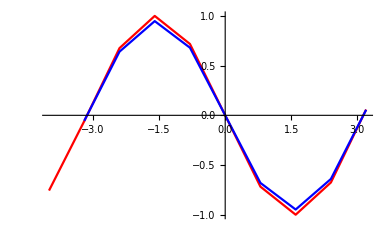
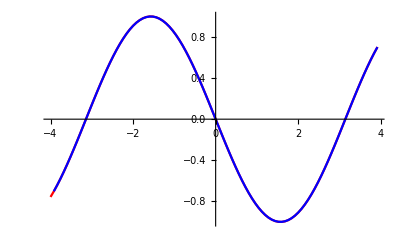
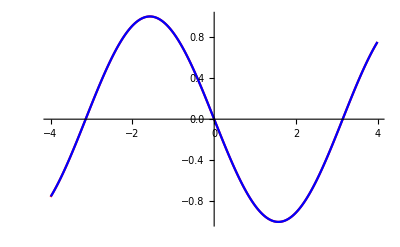

```mathematica
actual = Import["outputs/derivative-derivative-10.csv", "CSV"]
backward = Import["outputs/derivative-derivative-backward-10.csv", "CSV"];
n10 = ListLinePlot[{actual, backward}, PlotStyle->{Red, Blue}];
actual = Import["outputs/derivative-derivative-100.csv", "CSV"];
backward = Import["outputs/derivative-derivative-backward-100.csv", "CSV"];
n100 = ListLinePlot[{actual, backward}, PlotStyle->{Red, Blue}];
actual = Import["outputs/derivative-derivative-1000.csv", "CSV"];
backward = Import["outputs/derivative-derivative-backward-1000.csv", "CSV"];
n1000 = ListLinePlot[{actual, backward}, PlotStyle->{Red, Blue}];
{n10, n100, n1000}
```